```mathematica
α =  1/137.04;
```

Скорость частицы S^+(m) в системе центра масс S^+S^--пары в зависимости от отношения m/M:

```mathematica
V[mRatio_] :=Sqrt[1 - 4 mRatio^2 ]
```

Скорость частицы S^+(m) относительно S^- в зависимости от отношения m/M:

```mathematica
Vrel[mRatio_] := V[mRatio]/(1 - 2 mRatio^2)
```

Фактор Гамова-Зоммерфельда-Сахарова:

```mathematica
GSS[v_] := (2 Pi α/v)/(1-Exp[-2 Pi α/v]);
```

```mathematica
MB = 5279.66;

MBs = 5366.92;
me = 0.511;
mmu = 105.658; 

mtau = 1776.86;
```

```mathematica
Ksoft[frac_,v_]:=(2 frac)^((2 α/Pi)*(1/(4 v))*Log[(1+v)/(1-v)]);
```

```mathematica
Ksoft[0.06/MB,Vrel[mtau/MB]] GSS[Vrel[mtau/MB]]
```

0.974878

Фактор Кратера-Алстина-Сазджана:

```mathematica
CAS[v_] := (Abs[Gamma[Sqrt[1/4-α^2]+1/2+I α/v]/Gamma[Sqrt[1-4 α^2]+1]]^2)Exp[Pi α/v];
```

Фактор Фарри:

```mathematica
Furry[v_] := Exp[Pi α/v];
```

```mathematica
Plot[{Furry[V[x], Furry[Vrel[x]]]}, {x, 0., 0.5}]
```

-Graphics-

General::munfl: Exp[-4.58303×10^13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2.2648×10^13] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1.1192×10^13] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

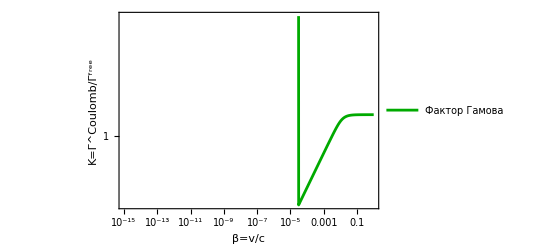

```mathematica
LogLogPlot[CAS[v]/ GSS[v], {v,10^-15,1},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,PlotLegends->{"Фактор Гамова","Метод Кратера-Сазджана"}, Frame->True, AxesLabel->{HoldForm[β=HoldForm[v]/c],HoldForm[Κ=Γ^Coulomb/Γ^free]},PlotStyle->{Blue,Red,Darker[Green]}]
```

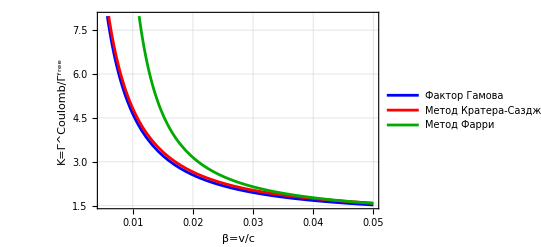

```mathematica
Plot[{GSS[v], 1.04 CAS[v], Furry[v]}, {v, 0.005,0.05},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,PlotLegends->{"Фактор Гамова","Метод Кратера-Сазджана", "Метод Фарри"}, Frame->True, AxesLabel->{HoldForm[β=HoldForm[v]/c],HoldForm[Κ=Γ^Coulomb/Γ^free]},PlotStyle->{Blue,Red,Darker[Green]}]
```

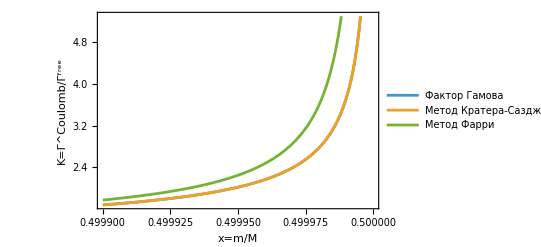

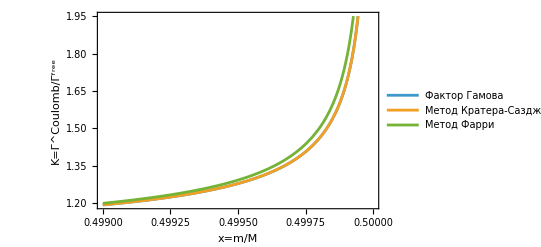

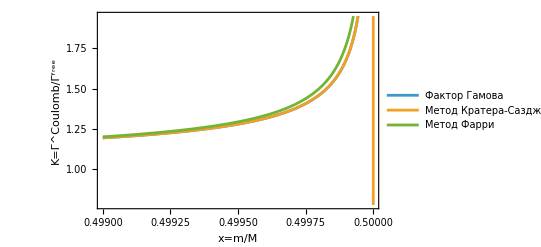

-Graphics-

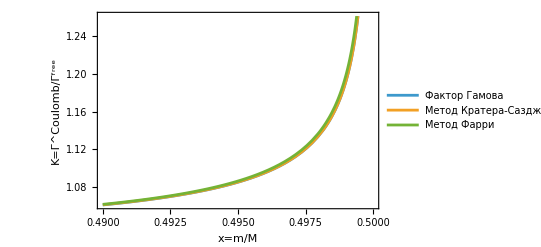

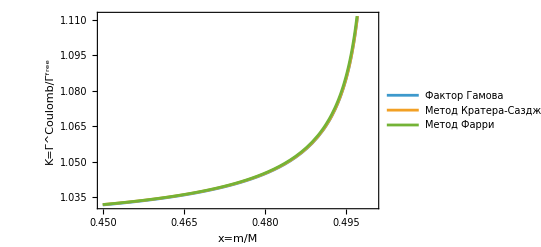

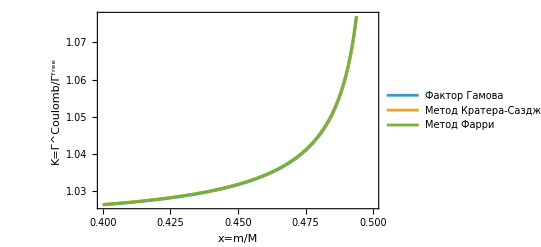

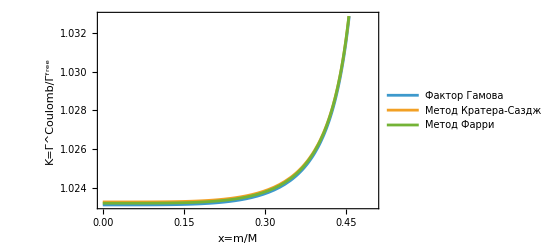

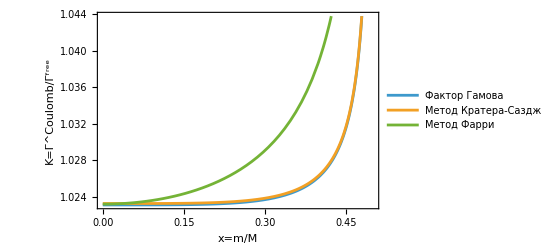

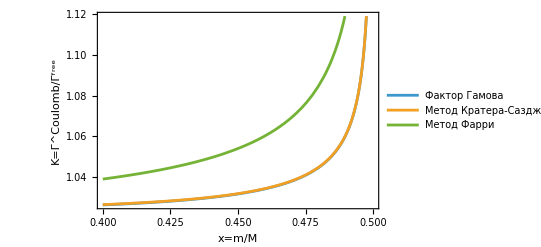

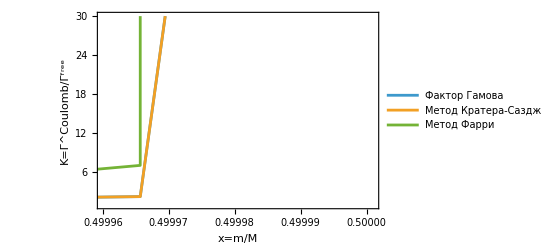

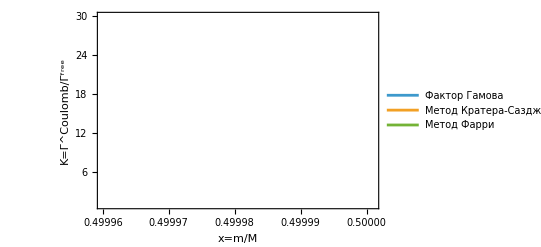

-Graphics-

-Graphics-

-Graphics-

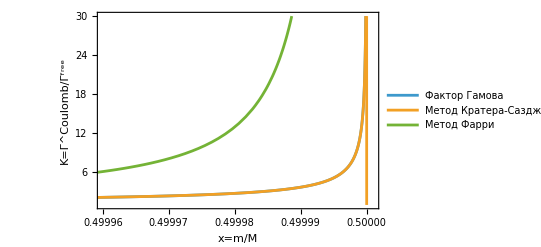

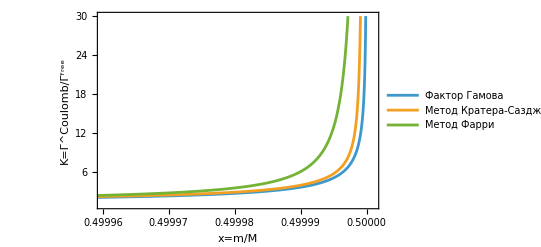

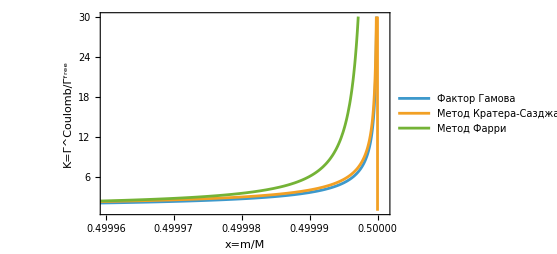

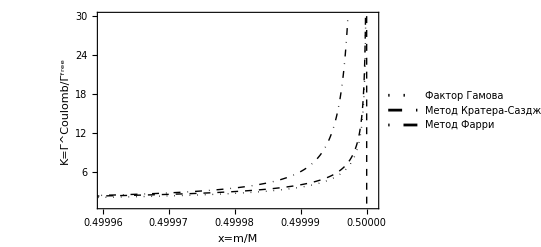

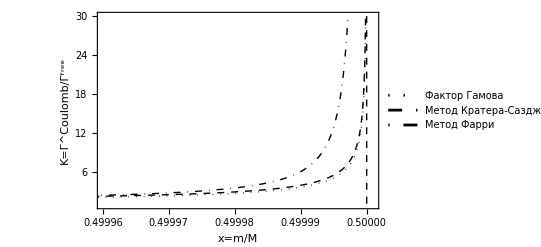

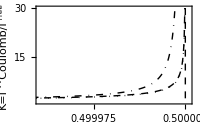

```mathematica
Plot[{GSS[Vrel[x]],  CAS[Vrel[x]], Furry[Vrel[x]]}, {x, 0.4999,0.4999999995},LabelStyle->{GrayLevel[0],Bold},PlotLegends->{"Фактор Гамова","Метод Кратера-Сазджана", "Метод Фарри"}, Frame->True, AxesLabel->{HoldForm[x = m/M],HoldForm[Κ=Γ^Coulomb/Γ^free]}]
```

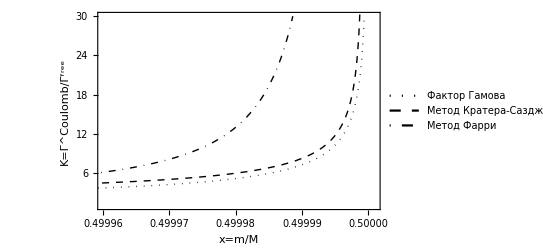

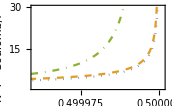

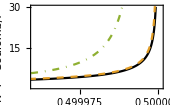

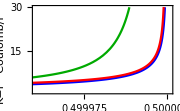

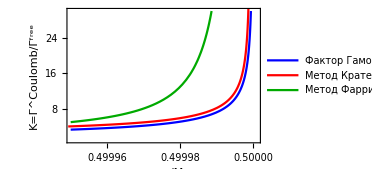

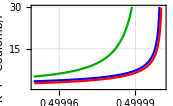

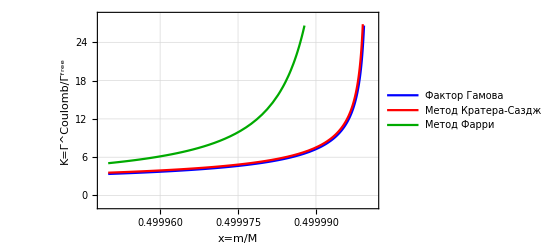

```mathematica
Plot[{(2 Pi α/Sqrt[1-4 (x/10000+0.5)^2])/(1-Exp[-2 Pi α/Sqrt[1-4 (x/10000+0.5)^2]]), (Abs[Gamma[Sqrt[1/4-α^2]+1/2+I α/Sqrt[1-4 (x/10000+0.5)^2]]/Gamma[Sqrt[1-4 α^2]+1]]^2)Exp[Pi α/Sqrt[1-4 (x/10000+0.5)^2]], Exp[Pi α/Sqrt[1-4 (x/100000+0.5)^2]]}, {x, -10,0},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,PlotLegends->{"Фактор Гамова","Метод Кратера-Сазджана", "Метод Фарри"}, Frame->True, AxesLabel->{HoldForm[x = m/M],HoldForm[Κ=Γ^Coulomb/Γ^free]},PlotStyle->{Blue,Red,Darker[Green]},PlotRange-> {{-10,0.1},{1,30}}]
```

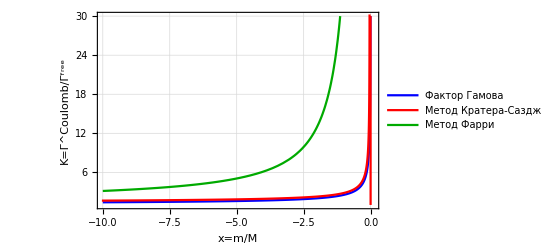

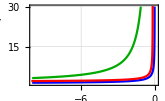

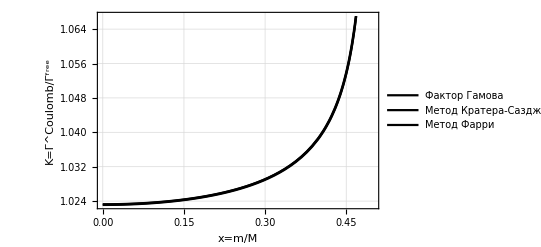

```mathematica
Plot[{(2 Pi α/Sqrt[1-4 x^2])/(1-Exp[-2 Pi α/Sqrt[1-4 x^2]]), (Abs[Gamma[Sqrt[1/4-α^2]+1/2+I α/Sqrt[1-4 x^2]]/Gamma[Sqrt[1-4 α^2]+1]]^2)Exp[Pi α/Sqrt[1-4 x^2]], Exp[Pi α/Sqrt[1-4 x^2]]}, {x, 0,0.5},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,PlotLegends->{"Фактор Гамова","Метод Кратера-Сазджана", "Метод Фарри"}, Frame->True, AxesLabel->{HoldForm[x = m/M],HoldForm[Κ=Γ^Coulomb/Γ^free]},PlotStyle->{Black,Black,Black}]
```

```mathematica
(*Константы*)α=1/137.04;
MB=5279.66;    (*МэВ*)
MBs=5366.92;   (*МэВ*)
me=0.511;      (*МэВ*)
mmu=105.658;   (*МэВ*)
mtau=1776.86;  (*МэВ*)

(*Вспомогательные функции*)
Vrel[m_,MB_]:=Module[{ratio=m/MB},Sqrt[1-4 ratio^2]/(1-2 ratio^2)]
KCoulomb[v_]:=(2 Pi α/v)/(1-Exp[-2 Pi α/v])
Ksoft[ΔE_,v_,MB_]:=(2 ΔE/MB)^((2 α/Pi)*(1/(4 v))*Log[(1+v)/(1-v)])

(*Список распадов:{название,масса мезона,масса лептона}*)
decays={{"Bs → μμ",MBs,mmu},{"B0 → μμ",MB,mmu},{"Bs → ee",MBs,me},{"B0 → ee",MB,me},{"Bs → ττ",MBs,mtau},{"B0 → ττ",MB,mtau}};

(*Значения обрезания ΔE в МэВ*)
ΔElist={50,100,500};  (*0.05,0.1,0.5 GeV*)

(*Заголовок таблицы*)
Print["Decay\t\t𝓀_C\t\t𝓀_{QED}(0.05)\t𝓀_{QED}(0.1)\t𝓀_{QED}(0.5)"];
Print["---------------------------------------------------------------------------------------------"];

(*Цикл по распадам*)
Do[{name,mB,mℓ}=decays[[i]];
v=Vrel[mℓ,mB];
kC=KCoulomb[v];
(*Вычисляем Ksoft и KQED для каждого ΔE*)kQEDlist=Table[kC*Ksoft[ΔE,v,mB],{ΔE,ΔElist}];
(*Вывод результата с округлением до 4 знаков*)Print[StringForm["``\t\t``\t\t``\t\t``\t\t``",name,NumberForm[kC,{Infinity,4}],NumberForm[kQEDlist[[1]],{Infinity,4}],NumberForm[kQEDlist[[2]],{Infinity,4}],NumberForm[kQEDlist[[3]],{Infinity,4}]]],{i,Length[decays]}];
```

Decay		𝓀_C		𝓀_{QED}(0.05)	𝓀_{QED}(0.1)	𝓀_{QED}(0.5)

---------------------------------------------------------------------------------------------

Bs → μμ		1.0231		0.9514		0.9635		0.9922

B0 → μμ		1.0231		0.9520		0.9640		0.9926

Bs → ee		1.0231		0.8648		0.8905		0.9531

B0 → ee		1.0231		0.8611		0.8874		0.9517

Bs → ττ		1.0241		1.0051		1.0084		1.0160

B0 → ττ		1.0242		1.0056		1.0088		1.0163

```mathematica
kQEDlist
```

{1.0056,1.00882,1.01634}

```mathematica
Ksoft[60/MB,Vrel[mtau/MB]]
```

0.982695